# Spatially Adaptive Finite Volume Method For Moment Models

This Mathematica file implements a spatially adaptive finite volume method for moment models. The spatial adaptivity allows the simulation to use a different number of moments (and so different models) in different parts of the domain. Currently, the setting is the following: the domain is divided in N subdomains. 
--------------------------------------------------------------------------------------------
TODO:
- Make source term matrices global variables
- Dynamic plotting of the current time step
- Dynamic plotting of the variables at the same time
- Include multiple boundary interfaces

## Construction of Spatially Adaptive Moment Model

Construction of the spatial discretization matrix of the models. The construction is split into transport part (Roe matrix and viscosity matrix) and source term part (relaxation).

### Source Term

Computation of source term.

#### Extended vector models

Construction of the source term matrix for the models using the extended vector.

```mathematica
ConstructSourceTerm[]:=Block[{SourceTermVector,moments,SourceTermVectorCell,nxL,nxR},
SourceTermVector={};
nxR=-1;
For[k=1,k<=Length[MomentsDomainDecomposition],k++,
nxL=nxR+1;
nxR=DiscretizedDomainDecomposition[[k]]-2;
SourceTermVectorCell={0,0,0};
moments=MomentsDomainDecomposition[[k]];
For[j=4,j<=moments,j++,
SourceTermVectorCell=Append[SourceTermVectorCell,1];
];
For[i=nxL,i<=nxR,i++,
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[i]]*SourceTermVectorCell];
];
];
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[n-1]]*SourceTermVectorCell];
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[n]]*SourceTermVectorCell];
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[n+1]]*SourceTermVectorCell];

(* Obtain source term matrix *)
SourceTermMatrix=DiagonalMatrix[SourceTermVector];

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];
SourceTermMatrixExp=DiagonalMatrix[SourceTermVector];
];
```

#### Non-square matrix models (THIS METHOD IS NOT USED ANYMORE)

Construction of the source term for the model that used non-square matrices.

```mathematica
ConstructSourceTermNonSquare[]:=Block[{SourceMatrixLeft,SourceMatrixRight,SourceTermVectorLeft,SourceTermVectorRight,SourceTermVector},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)
SourceTermVector={};
nxR=-1;
For[k=1,k<=Length[MomentsDomainDecomposition],k++,
nxL=nxR+1;
nxR=DiscretizedDomainDecomposition[[k]];
SourceTermVectorCell={0,0,0};
moments=MomentsDomainDecomposition[[k]];
For[j=4,j<=moments,j++,
SourceTermVectorCell=Append[SourceTermVectorCell,1];
];
For[i=nxL,i<=nxR,i++,
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[i]]*SourceTermVectorCell];
];
];
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[n-1]]*SourceTermVectorCell];
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[n]]*SourceTermVectorCell];
SourceTermVector=Join[SourceTermVector,-1/Relaxation[xs[n+1]]*SourceTermVectorCell];

(* Obtain source term matrix *)
SourceTermMatrixNonSquare=DiagonalMatrix[SourceTermVector];

(* Obtain Exponential of source term vector *)
SourceTermVector=Exp[SourceTermVector*dt];

SourceTermMatrixNonSquareExp=DiagonalMatrix[SourceTermVector];
];
```

### Construction of model at the interface between the two subdomains

There are different options for the model we use in the cell directly right of the interface between the left and the right subdomains, in which a different number of moments is used.

#### Using a modified system matrix at the boundary interface

```mathematica
(* Here we use a modified Roe linearization at the boundary interface *) (* THIS METHOD HAS NOT BEEN TESTED YET *)
modifiedRoeMatrixAtInterface[]:=Block[{momentsLeft,momentsRight,numberOfMomentsDifference,ALeft,ARight,QLeft,QRight},

For[k=1,k<Length[MomentsDomainDecomposition],k++,
momentsLeft=MomentsDomainDecomposition[[k]];
momentsRight=MomentsDomainDecomposition[[k+1]];
numberOfMomentsDifference=momentsRight-momentsLeft;
ALeft=SparseArray[{{i_,j_}/;i-j==1:>1,{i_,j_}/;j-i==1:>i},{momentsLeft,momentsLeft}];
QLeft=IdentityMatrix[momentsLeft];
ARight=SparseArray[{{i_,j_}/;i-j==1:>1,{i_,j_}/;j-i==1:>i},{momentsRight,momentsRight}];
QRight=IdentityMatrix[momentsRight];
nxL=DiscretizedDomainDecomposition[[k]];

RoeModifiedBlockMatrix[[nxL+2,nxL+1]]=-ARight;
RoeModifiedBlockMatrix[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeModifiedBlockMatrix[[nxL+2,nxL+3]]=ARight;
ViscosityModifiedBlockMatrix[[nxL+2,nxL+1]]=-QRight;
ViscosityModifiedBlockMatrix[[nxL+2,nxL+2]]=2*QRight;
ViscosityModifiedBlockMatrix[[nxL+2,nxL+3]]=-QRight;

RoeModifiedBlockMatrix[[nxL+1,nxL]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
RoeModifiedBlockMatrix[[nxL+1,nxL+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ARight;
RoeModifiedBlockMatrix[[nxL+1,nxL+2]]=ARight;
ViscosityModifiedBlockMatrix[[nxL+1,nxL]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityModifiedBlockMatrix[[nxL+1,nxL+1]]=ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]+QRight;
ViscosityModifiedBlockMatrix[[nxL+1,nxL+2]]=-QRight;

RoeModifiedBlockMatrix[[nxL,nxL-1]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
RoeModifiedBlockMatrix[[nxL,nxL]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeModifiedBlockMatrix[[nxL,nxL+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityModifiedBlockMatrix[[nxL,nxL-1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
ViscosityModifiedBlockMatrix[[nxL,nxL]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityModifiedBlockMatrix[[nxL,nxL+1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];

];
];
```

#### Using non-square matrices (THIS METHOD IS NOT USED ANYMORE0)

```mathematica
nonSquareMatricesAtInterface[]:=Block[{momentsLeft,momentsRight,numberOfMomentsDifference,ALeft,ARight,QLeft,QRight},

For[j=1,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareBlockMatrices[[1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

(* Rows corresponding to moment model of order ML *)
For[i=2,i<=nxL,i++,
RoeNonSquareBlockMatrices[[i,i-1]]=-ALeft;
RoeNonSquareBlockMatrices[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeNonSquareBlockMatrices[[i,i+1]]=ALeft;
ViscosityNonSquareBlockMatrices[[i,i-1]]=-QLeft;
ViscosityNonSquareBlockMatrices[[i,i]]=2*QLeft;
ViscosityNonSquareBlockMatrices[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];
];

RoeNonSquareBlockMatrices[[nxL+1,nxL]]=-ALeft;
RoeNonSquareBlockMatrices[[nxL+1,nxL+1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeNonSquareBlockMatrices[[nxL+1,nxL+2]]=ARight[[;;-(numberOfMomentsDifference+1),;;]];
ViscosityNonSquareBlockMatrices[[nxL+1,nxL]]=-QLeft;
ViscosityNonSquareBlockMatrices[[nxL+1,nxL+1]]=2*QLeft;
ViscosityNonSquareBlockMatrices[[nxL+1,nxL+2]]=-QRight[[;;-(numberOfMomentsDifference+1),;;]];
For[j=1,j<nxL,j++,
RoeNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[j=nxL+3,j<=n+2,j++,
RoeNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
ViscosityNonSquareBlockMatrices[[nxL+1,j]]=ConstantArray[0,{momentsLeft,momentsRight}];
];

RoeNonSquareBlockMatrices[[nxL+2,nxL+1]]=-ARight[[;;,;;-(numberOfMomentsDifference+1)]];
RoeNonSquareBlockMatrices[[nxL+2,nxL+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeNonSquareBlockMatrices[[nxL+2,nxL+3]]=ARight;
ViscosityNonSquareBlockMatrices[[nxL+2,nxL+1]]=-QRight[[;;,;;-(numberOfMomentsDifference+1)]];
ViscosityNonSquareBlockMatrices[[nxL+2,nxL+2]]=2*QRight;
ViscosityNonSquareBlockMatrices[[nxL+2,nxL+3]]=-QRight;
For[j=1,j<=nxL,j++,
RoeNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];
For[j=nxL+4,j<=n+2,j++,
RoeNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[nxL+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[i=nxL+3,i<n+2,i++,
RoeNonSquareBlockMatrices[[i,i-1]]=-ARight;
RoeNonSquareBlockMatrices[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeNonSquareBlockMatrices[[i,i+1]]=ARight;

ViscosityNonSquareBlockMatrices[[i,i-1]]=-QRight;
ViscosityNonSquareBlockMatrices[[i,i]]=2*QRight;
ViscosityNonSquareBlockMatrices[[i,i+1]]=-QRight;

For[j=1,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+2,j<i-1,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];

For[j=i+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

For[j=1,j<=nxL+1,j++,
RoeNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

For[j=nxL+2,j<=n+2,j++,
RoeNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityNonSquareBlockMatrices[[n+2,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];
```

### Construction matrix

Computation of the numerical viscosity matrix with Roe matrix as input

```mathematica
ComputeQ[RoeMatrix_]:=Block[{dimension,},(* Make QMatrix local variable *)
dimension=Dimensions[RoeMatrix][[1]];
QMatrix=IdentityMatrix[dimension];
{QMatrix}(* Define more numerical viscosity matrices *)
]
```

Construction of the Roe matrix and the viscosity matrix.

```mathematica
ConstructMatrix[]:=Block[{nxL,nxR,ALeft,ARight,momentsLeft,momentsRight,numberOfMomentsDifference,QLeft,QRight,nxLIteration,nxRIteration,momentsIteration},

(* Initialize block matrices for the different models *)

RoeBlockMatrix=ConstantArray[0,{n+2,n+2}];
ViscosityBlockMatrix=ConstantArray[0,{n+2,n+2}];

RoeModifiedBlockMatrix = ConstantArray[0,{n+2,n+2}];
ViscosityModifiedBlockMatrix=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First three cells are constructed separately *)
momentsLeft=MomentsDomainDecomposition[[1]];
nxRIteration=DiscretizedDomainDecomposition[[1]]-1;
ALeft=SparseArray[{{i_,j_}/;i-j==1:>1,{i_,j_}/;j-i==1:>i},{momentsLeft,momentsLeft}];
QLeft=IdentityMatrix[momentsLeft];
For[j=1,j<=nxRIteration,j++,
RoeBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[m=2,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[1,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
];
RoeBlockMatrix[[1,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[1,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[1,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[1,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[1,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[1,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];

nxRIteration=DiscretizedDomainDecomposition[[1]]-1;
RoeBlockMatrix[[2,1]]=-ALeft;
RoeBlockMatrix[[2,2]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeBlockMatrix[[2,3]]=ALeft;
ViscosityBlockMatrix[[2,1]]=-QLeft;
ViscosityBlockMatrix[[2,2]]=2*QLeft;
ViscosityBlockMatrix[[2,3]]=-QLeft;
For[j=4,j<=nxRIteration,j++,
RoeBlockMatrix[[2,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[2,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[m=2,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[2,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[2,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
];
RoeBlockMatrix[[2,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[2,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[2,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[2,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[2,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[2,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];

nxRIteration=DiscretizedDomainDecomposition[[1]]-1;
RoeBlockMatrix[[3,1]]=ConstantArray[0,{momentsLeft,momentsLeft}];;
RoeBlockMatrix[[3,2]]=-ALeft;
RoeBlockMatrix[[3,3]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeBlockMatrix[[3,4]]=ALeft;
ViscosityBlockMatrix[[3,1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[3,2]]=-QLeft;
ViscosityBlockMatrix[[3,3]]=2*QLeft;
ViscosityBlockMatrix[[3,4]]=-QLeft;
For[j=5,j<=nxRIteration,j++,
RoeBlockMatrix[[3,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[3,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
For[m=2,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[3,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[3,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
];
RoeBlockMatrix[[3,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[3,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[3,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[3,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[3,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[3,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];



nxR=1;
For[k=1,k<Length[MomentsDomainDecomposition],k++, (* Last subdomain is treated separately *)
momentsLeft=MomentsDomainDecomposition[[k]];
momentsRight=MomentsDomainDecomposition[[k+1]];
ALeft=SparseArray[{{i_,j_}/;i-j==1:>1,{i_,j_}/;j-i==1:>i},{momentsLeft,momentsLeft}];
ARight=SparseArray[{{i_,j_}/;i-j==1:>1,{i_,j_}/;j-i==1:>i},{momentsRight,momentsRight}];
If[momentsLeft==MaxMoment,CMax=Max[N[Abs[Eigenvalues[ALeft]]]];];
QLeft=IdentityMatrix[momentsLeft];
QRight=IdentityMatrix[momentsRight];
numberOfMomentsDifference=momentsRight-momentsLeft;
nxL=nxR+1;
nxR=DiscretizedDomainDecomposition[[k]];

For[i=nxL+2,i<nxR-1,i++,(* Row-by-row construction of the matrix *)
nxRIteration=0;
For[m=1,m<k,m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
];
For[j=nxL-1,j<i-1,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
RoeBlockMatrix[[i,i-1]]=-ALeft;
RoeBlockMatrix[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeBlockMatrix[[i,i+1]]=ALeft;
ViscosityBlockMatrix[[i,i-1]]=-QLeft;
ViscosityBlockMatrix[[i,i]]=2*QLeft;
ViscosityBlockMatrix[[i,i+1]]=-QLeft;
For[j=i+2,j<=nxR-1,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
nxRIteration=nxR-1;
For[m=k+1,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
];
RoeBlockMatrix[[i,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[i,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[i,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[i,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[i,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[i,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
(* Row nxR-1 (corresponds to vector nxR-2 because of the introduced ghost rows *) 
nxRIteration=0;
For[m=1,m<k,m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR-1,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[nxR-1,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
];

For[j=nxL-1,j<nxR-2,j++,
RoeBlockMatrix[[nxR-1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityBlockMatrix[[nxR-1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

RoeBlockMatrix[[nxR-1,nxR-2]]=-ALeft;
RoeBlockMatrix[[nxR-1,nxR-1]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeBlockMatrix[[nxR-1,nxR]]=ArrayPad[ALeft,{{0,0},{0,numberOfMomentsDifference}}];
ViscosityBlockMatrix[[nxR-1,nxR-2]]=-QLeft;
ViscosityBlockMatrix[[nxR-1,nxR-1]]=2*QLeft;
ViscosityBlockMatrix[[nxR-1,nxR]]=-ArrayPad[QLeft,{{0,0},{0,numberOfMomentsDifference}}];

nxRIteration=nxR;
For[m=k+1,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR-1,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[nxR-1,j]]=ConstantArray[0,{momentsLeft,momentsIteration}];
];
];
RoeBlockMatrix[[nxR-1,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[nxR-1,n]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[nxR-1,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[nxR-1,n+1]]=ConstantArray[0,{momentsLeft,momentsIteration}];
RoeBlockMatrix[[nxR-1,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];
ViscosityBlockMatrix[[nxR-1,n+2]]=ConstantArray[0,{momentsLeft,momentsIteration}];

(* Row nxR (corresponds to vector nxR-1 because of the introduced ghost rows) *)

nxRIteration=0;
For[m=1,m<k,m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];

For[j=nxL-1,j<nxR-1,j++,
RoeBlockMatrix[[nxR,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[nxR,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

RoeBlockMatrix[[nxR,nxR-1]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,0}}];
RoeBlockMatrix[[nxR,nxR]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeBlockMatrix[[nxR,nxR+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityBlockMatrix[[nxR,nxR-1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,0}}];
ViscosityBlockMatrix[[nxR,nxR]]=2*ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityBlockMatrix[[nxR,nxR+1]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];

nxRIteration=nxR+1;
For[m=k+1,m<=Length[MomentsDomainDecomposition],m++,(* Here I need to make some changes as the matrices at the interface are not necessarily zero-blocks *)
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];
RoeBlockMatrix[[nxR,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[nxR,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[nxR,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];

(* Row nxR+1 (correspond to vector nxR because of the introduced  ghost rows *)

nxRIteration=0;
For[m=1,m<k,m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR+1,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+1,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];

For[j=nxL-1,j<=nxR-1,j++,
RoeBlockMatrix[[nxR+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[nxR+1,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];

RoeBlockMatrix[[nxR+1,nxR]]=-ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
RoeBlockMatrix[[nxR+1,nxR+1]]=ArrayPad[ALeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]-ARight;
RoeBlockMatrix[[nxR+1,nxR+2]]=ARight;
ViscosityBlockMatrix[[nxR+1,nxR]]=-ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}];
ViscosityBlockMatrix[[nxR+1,nxR+1]]=ArrayPad[QLeft,{{0,numberOfMomentsDifference},{0,numberOfMomentsDifference}}]+QRight;
ViscosityBlockMatrix[[nxR+1,nxR+2]]=-QRight;

nxRIteration=nxR+2;
For[m=k+1,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR+1,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+1,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];
RoeBlockMatrix[[nxR+1,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+1,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[nxR+1,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+1,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[nxR+1,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+1,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];


(* Row nxR+2 (corresponds to vector nxR+1 because of the introduced ghost rows *)
nxRIteration=0;
For[m=1,m<k,m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR+2,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+2,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];

For[j=nxL-1,j<nxR,j++,
RoeBlockMatrix[[nxR+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
ViscosityBlockMatrix[[nxR+2,j]]=ConstantArray[0,{momentsRight,momentsLeft}];
];
RoeBlockMatrix[[nxR+2,nxR]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[nxR+2,nxR]]=ConstantArray[0,{momentsRight,momentsRight}];

RoeBlockMatrix[[nxR+2,nxR+1]]=-ARight;
RoeBlockMatrix[[nxR+2,nxR+2]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeBlockMatrix[[nxR+2,nxR+3]]=ARight;
ViscosityBlockMatrix[[nxR+2,nxR+1]]=-QRight;
ViscosityBlockMatrix[[nxR+2,nxR+2]]=2*QRight;
ViscosityBlockMatrix[[nxR+2,nxR+3]]=-QRight;

nxRIteration=nxR+3;
For[m=k+1,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[nxR+2,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+2,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];
RoeBlockMatrix[[nxR+2,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+2,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[nxR+2,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+2,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[nxR+2,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[nxR+2,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];
];

(* Last subdomain is constructed separately *)
If[momentsRight==MaxMoment,CMax=Max[N[Abs[Eigenvalues[ARight]]]];];
For[i=nxR+3,i<=n+1,i++,
nxRIteration=0;
For[m=1,m<Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];
For[j=nxRIteration+1,j<i-1,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
RoeBlockMatrix[[i,i-1]]=-ARight;
RoeBlockMatrix[[i,i]]=ConstantArray[0,{momentsRight,momentsRight}];
RoeBlockMatrix[[i,i+1]]=ARight;
ViscosityBlockMatrix[[i,i-1]]=-QRight;
ViscosityBlockMatrix[[i,i]]=2*QRight;
ViscosityBlockMatrix[[i,i+1]]=-QRight;
For[j=i+2,j<=n+2,j++,
RoeBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
ViscosityBlockMatrix[[i,j]]=ConstantArray[0,{momentsRight,momentsRight}];
];
];

(* Last row is a ghost row *)
nxRIteration=0;
For[m=1,m<=Length[MomentsDomainDecomposition],m++,
nxLIteration=nxRIteration+1;
nxRIteration=DiscretizedDomainDecomposition[[m]]-1;
momentsIteration=MomentsDomainDecomposition[[m]];
For[j=nxLIteration,j<=nxRIteration,j++,
RoeBlockMatrix[[n+2,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[n+2,j]]=ConstantArray[0,{momentsRight,momentsIteration}];
];
];
RoeBlockMatrix[[n+2,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[n+2,n]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[n+2,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[n+2,n+1]]=ConstantArray[0,{momentsRight,momentsIteration}];
RoeBlockMatrix[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];
ViscosityBlockMatrix[[n+2,n+2]]=ConstantArray[0,{momentsRight,momentsIteration}];

(* Call methods for using a modified Roe matrix at the boundary interface and using the model with non-square matrices at the interface. *)
RoeModifiedBlockMatrix=RoeBlockMatrix;
ViscosityModifiedBlockMatrix=ViscosityBlockMatrix;
(*modifiedRoeMatrixAtInterface[];*)

(* Obtain full matrices from their block form *)
RoeMatrix = ArrayFlatten[RoeBlockMatrix];
ViscosityMatrix = ArrayFlatten[ViscosityBlockMatrix];

RoeModifiedMatrix = ArrayFlatten[RoeModifiedBlockMatrix];
ViscosityModifiedMatrix = ArrayFlatten[ViscosityModifiedBlockMatrix];

(* Choose time step *)
dt=0.1 dx/CMax;

(* Call the method that construct the source term *)
ConstructSourceTerm[];

(* Obtain transport part of spatial discretization matrix from Roe block matrix and viscosity block matrix *)

BigAMatrixBlock=-1.0/(2*dx)*(RoeBlockMatrix+ViscosityBlockMatrix);
BigAMatrix = -1.0/(2*dx)*(RoeMatrix+ViscosityMatrix);

BigAMatrixBlockModified=-1.0/(2*dx)*(RoeModifiedBlockMatrix+ViscosityModifiedBlockMatrix);
BigAMatrixModified = -1.0/(2*dx)*(RoeModifiedMatrix+ViscosityModifiedMatrix);

];
```

## Construction of Reference Solution

As reference solution, we consider the numerical solution we obtain if we used the bigger matrix in the whole domain.

### Source Term

Construction of the source term matrix for the reference system.

```mathematica
ConstructSourceTermReference[]:=Block[{SourceTermVectorReference,SourceTermVectorRight},
SourceTermVectorRight={0,0,0};

For[i=4,i<=MaxMoment,i++,
SourceTermVectorRight=Append[SourceTermVectorRight,1];
];

SourceTermVectorReference={};
For[i=0,i<=n+1,i++,
SourceTermVectorReference=Join[SourceTermVectorReference,-1/Relaxation[xs[i]]*SourceTermVectorRight];
];

(* Obtain source term matrix *)
SourceTermMatrixReference=DiagonalMatrix[SourceTermVectorReference];

(* Obtain Exponential of source term vector *)
SourceTermVectorReference=Exp[SourceTermVectorReference*dt];

SourceTermMatrixReferenceExp=DiagonalMatrix[SourceTermVectorReference];
];
```

### Construction matrix

Construction of the Roe matrix and the viscosity matrix for the reference system.

```mathematica
ConstructMatrixReference[]:=Block[{RoeReferenceBlock,ViscosityReferenceBlock,A,Q},
RoeReferenceBlock = ConstantArray[0,{n+2,n+2}];
ViscosityReferenceBlock=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)
A=SparseArray[{{i_,j_}/;i-j==1:>1,{i_,j_}/;j-i==1:>i},{MaxMoment,MaxMoment}];
Q=IdentityMatrix[MaxMoment];

(* First row is a ghost row *)
For[j=1,j<=n+2,j++,
RoeReferenceBlock[[1,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
ViscosityReferenceBlock[[1,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
];

(* All rows apart from the first and the last *)
For[i=2,i<=n+1,i++,
RoeReferenceBlock[[i,i-1]]=-A;
RoeReferenceBlock[[i,i]]=ConstantArray[0,{MaxMoment,MaxMoment}];
RoeReferenceBlock[[i,i+1]]=A;
ViscosityReferenceBlock[[i,i-1]]=-Q;
ViscosityReferenceBlock[[i,i]]=2*Q;
ViscosityReferenceBlock[[i,i+1]]=-Q;

For[j=1,j<i-1,j++,
RoeReferenceBlock[[i,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
ViscosityReferenceBlock[[i,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
];

For[j=i+2,j<=n+2,j++,
RoeReferenceBlock[[i,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
ViscosityReferenceBlock[[i,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
];
];

(* Last rows are ghost rows *)
For[j=1,j<=n+2,j++,
RoeReferenceBlock[[n+2,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
ViscosityReferenceBlock[[n+2,j]]=ConstantArray[0,{MaxMoment,MaxMoment}];
];

(* Call the method that constructs the source term for the reference system *)
ConstructSourceTermReference[];

(* Obtain full Roe matrix and full viscosity matrix from their block form *)
RoeReference = ArrayFlatten[RoeReferenceBlock];
ViscosityReference = ArrayFlatten[ViscosityReferenceBlock];

(* Obtain transport part of spatial discretization matrix for the reference system from Roe block matrix and viscosity block matrix *)
BigAMatrixReferenceBlock=-1.0/(2*dx)*(RoeReferenceBlock+ViscosityReferenceBlock);
BigAMatrixReference = -1.0/(2*dx)*(RoeReference+ViscosityReference);
];
```

## Construction of low-order Solution

The low-order numerical approximation is obtained by using the low order model in the entire domain.

### Source Term

Construction of the source term matrix for the reference system.

```mathematica
ConstructSourceTermLowOrder[]:=Block[{SourceTermVectorLowOrder,SourceTermVectorLeft},
(* For the RHS source term, we assume a BGK-type operator and we assume that the source term matrix is a diagonal matrix *)

SourceTermVectorLeft={0,0,0};

For[i=4,i<=momentsLeft,i++,
SourceTermVectorLeft=Append[SourceTermVectorLeft,1];
];

SourceTermVectorLowOrder={};
For[i=0,i<=n+1,i++,
SourceTermVectorLowOrder=Join[SourceTermVectorLowOrder,-1/Relaxation[xs[i]]*SourceTermVectorLeft];
];
(* Obtain source term matrix *)
SourceTermMatrixLowOrder=DiagonalMatrix[SourceTermVectorLowOrder];

(* Obtain Exponential of source term vector *)
SourceTermVectorLowOrder=Exp[SourceTermVectorLowOrder*dt];

SourceTermMatrixLowOrderExp=DiagonalMatrix[SourceTermVectorLowOrder];
];
```

### Construction matrix

Construction of the Roe matrix and the viscosity matrix for the low-order numerical approximation.

```mathematica
ConstructMatrixLowOrder[]:=Block[{RoeLowOrderBlock,ViscosityLowOrderBlock},
RoeLowOrderBlock = ConstantArray[0,{n+2,n+2}];
ViscosityLowOrderBlock=ConstantArray[0,{n+2,n+2}];

(* CREATE THE SPATIAL DISCRETIZATION MATRIX BLOCK BY BLOCK *)

(* First row is a ghost row *)
For[j=1,j<=n+2,j++,
RoeLowOrderBlock[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityLowOrderBlock[[1,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

(* All rows apart from the first and the last *)
For[i=2,i<=n+1,i++,
RoeLowOrderBlock[[i,i-1]]=-ALeft;
RoeLowOrderBlock[[i,i]]=ConstantArray[0,{momentsLeft,momentsLeft}];
RoeLowOrderBlock[[i,i+1]]=ALeft;
ViscosityLowOrderBlock[[i,i-1]]=-QLeft;
ViscosityLowOrderBlock[[i,i]]=2*QLeft;
ViscosityLowOrderBlock[[i,i+1]]=-QLeft;

For[j=1,j<i-1,j++,
RoeLowOrderBlock[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityLowOrderBlock[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

For[j=i+2,j<=n+2,j++,
RoeLowOrderBlock[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityLowOrderBlock[[i,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];
];

(* Last rows are ghost rows *)
For[j=1,j<=n+2,j++,
RoeLowOrderBlock[[n+2,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
ViscosityLowOrderBlock[[n+2,j]]=ConstantArray[0,{momentsLeft,momentsLeft}];
];

(* Call the method that constructs the source term for the reference system *)
ConstructSourceTermLowOrder[];

(* Obtain full Roe matrix and full viscosity matrix from their block form *)
RoeLowOrder= ArrayFlatten[RoeLowOrderBlock];
ViscosityLowOrder = ArrayFlatten[ViscosityLowOrderBlock];

(* Obtain transport part of spatial discretization matrix for the reference system from Roe block matrix and viscosity block matrix *)
BigAMatrixLowOrderBlock=-1.0/(2*dx)*(RoeLowOrderBlock+ViscosityLowOrderBlock);
BigAMatrixLowOrder = -1.0/(2*dx)*(RoeLowOrder+ViscosityLowOrder);
];
```

## Simulation Setup

Initialize model: construct vector with initial values, set parameters and call the spatial discretization matrices constructor functions.

### Domain decomposition

```mathematica
DomainDecomposition[domainDecompositionList_]:=(
DiscretizedDomainDecomposition=List[];
AppendTo[DiscretizedDomainDecomposition,Round[(domainDecompositionList[[1]]-x1)/(x2-x1)*n]];
For[i=2,i<=Length[domainDecompositionList],i++,
AppendTo[DiscretizedDomainDecomposition,DiscretizedDomainDecomposition[[i-1]]+Round[(domainDecompositionList[[i]]-domainDecompositionList[[i-1]])/(x2-x1)*n]];
];
AppendTo[DiscretizedDomainDecomposition,n];
);
```

### Construct vector with initial values for the extended vector models

Construct vector with the chosen initial values, for the models using the extended vector.

```mathematica
InitializeVector[paddingCondition_]:=
Block[{padding,nxLPrevious,nxL},
(* Construct initial vector for spatially adaptive simulation *)
Wraw={};
For[j=0,j<MomentsDomainDecomposition[[1]],j++,
Wraw=Append[Wraw,m0[j,xs[1]]];(* Zero order extrapolation for ghost cell *)
];
nxLPrevious=0;
For[k=1,k<Length[MomentsDomainDecomposition],k++,
nxL=DiscretizedDomainDecomposition[[k]];
For[i=nxLPrevious+1,i<nxL-1,i++,
For[j=0,j<MomentsDomainDecomposition[[k]],j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[j=0,j<MomentsDomainDecomposition[[k+1]],j++,
Wraw=Append[Wraw,m0[j,xs[nxL-1]]]; (* the cell with index nxL-1 needs to implement a boundary condition. The value for the last moment is overridden in the simulation function. *)
];
For[j=0,j<MomentsDomainDecomposition[[k]],j++,
Wraw=Append[Wraw,m0[j,xs[nxL]]];
];
If[paddingCondition=="zero",
For[j=MomentsDomainDecomposition[[k]],j<MomentsDomainDecomposition[[k+1]],j++,Wraw=Append[Wraw,0]]; (* set last moments in the extended vector to zero *)
];
If[paddingCondition=="neighbour",
For[j=MomentsDomainDecomposition[[k]],j<MomentsDomainDecomposition[[k+1]],j++,Wraw=Append[Wraw,m0[j,xs[nxL+1]]]]; (* set the last moments in the extended vector as the last moments of the neighbouring vector *)
];
nxLPrevious=DiscretizedDomainDecomposition[[k]];
];
For[i=DiscretizedDomainDecomposition[[-2]]+1,i<=n,i++,
For[j=0,j<MomentsDomainDecomposition[[-1]],j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[j=0,j<MomentsDomainDecomposition[[-1]],j++,
Wraw=Append[Wraw,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];

(* Construct initial vector for reference solution *)
WrawReference={};
For[j=0,j<MaxMoment,j++,
WrawReference=Append[WrawReference,m0[j,xs[1]]]; (* Zero order extrapolation for ghost cell *)
];
For[i=1,i<=n,i++,
For[j=0,j<MaxMoment,j++,
WrawReference=Append[WrawReference,m0[j,xs[i]]];
];
];
For[j=0,j<MaxMoment,j++,
WrawReference=Append[WrawReference,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];

(* Construct initial vector for low-order approximation *)
WrawLowOrder={};
For[j=0,j<MinMoment,j++,
WrawLowOrder=Append[WrawLowOrder,m0[j,xs[1]]]; (* Zero order extrapolation for ghost cell *)
];
For[i=1,i<=n,i++,
For[j=0,j<MaxMoment,j++,
WrawLowOrder=Append[WrawLowOrder,m0[j,xs[i]]];
];
];
For[j=0,j<MinMoment,j++,
WrawLowOrder=Append[WrawLowOrder,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];
];
```

### Construct vector with initial values for non-square matrix models (THIS METHOD IS NOT USED ANYMORE)

```mathematica
InitializeVectorNonSquare[momentsLeft_,momentsRight_]:=(

(* Construct initial vector for spatially adaptive simulation using non-square matrices *)
Wraw={};
For[j=0,j<momentsLeft,j++,
Wraw=Append[Wraw,m0[j,xs[1]]];(* Zero order extrapolation for ghost cell *)
];
For[i=1,i<=nxL,i++,
For[j=0,j<momentsLeft,j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[i=nxL+1,i<=n,i++,
For[j=0,j<momentsRight,j++,
Wraw=Append[Wraw,m0[j,xs[i]]];
];
];
For[j=0,j<momentsRight,j++,
Wraw=Append[Wraw,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];

(* Construct initial vector for reference solution *)
WrawReference={};
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[1]]]; (* Zero order extrapolation for ghost cell *)
];
For[i=1,i<=n,i++,
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[i]]];
];
];
For[j=0,j<momentsRight,j++,
WrawReference=Append[WrawReference,m0[j,xs[n]]]; (* Zero order extrapolation for ghost cell *)
];
);
```

### Set up model

Set spatial discretization parameters and call the spatial discretization matrix construction functions.

```mathematica
InitializeModel[]:=Block[{momentsLoop},
DomainDecomposition[domainDecompositionList];
dx=(x2-x1)/n;

MinMoment=Min[MomentsDomainDecomposition];
InitializeVector["neighbour"];
MaxMoment=Max[MomentsDomainDecomposition];

(* Initialize the collection of the moments *)
moments=Table[moment[i],{i,0,MaxMoment-1}];
momentsReference=Table[momentReference[i],{i,0,MaxMoment-1}];
momentsLowOrder=Table[momentLowOrder[i],{i,0,MinMoment-1}];;
momentsLoop=Table[moment[i],{i,0,MaxMoment-1}];
For[i=0,i<MaxMoment,i++,
moment[i]={};
momentReference[i]={};
];
For[i=0,i<MinMoment,i++,
momentLowOrder[i]={};
];

(* Initialize the sum of the moments to check conservation *)
momentsSum=Table[momentSum[i],{i,0,MaxMoment-1}];
momentsReferenceSum=Table[momentReferenceSum[i],{i,0,MaxMoment-1}];
momentsLowOrderSum=Table[momentLowOrderSum[i],{i,0,MinMoment-1}];
For[i=0,i<MaxMoment,i++,
momentSum[i]=0;
momentReferenceSum[i]=0;
];
For[i=0,i<MinMoment,i++,
momentLowOrderSum[i]=0;
];

ConstructMatrix[];
ConstructMatrixReference[];
ConstructMatrixLowOrder[];
];
```

```mathematica
(*InitializeModelNonSquare[nxL_,nxR_,x1_,x2_,momentsLeft_,momentsRight_]:=(

numberOfMomentsDifference=momentsRight-momentsLeft;
n=nxL+nxR;

dx=(x2-x1)/(nxL+nxR);
(* Create grid points *)
xs[i_]:=x1+dx*(i-0.5);

InitializeVectorNonSquare[momentsLeft,momentsRight];

(* Initialize the collection of the moments *)
moments=Table[moment[i],{i,0,momentsRight-1}];
momentsReference=Table[momentReference[i],{i,0,momentsRight-1}];
momentsLoop=Table[moment[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
moment[i]={};
momentReference[i]={};
];

(* Initialize the sum of the moments to check conservation *)
momentsSum=Table[momentSum[i],{i,0,momentsRight-1}];
For[i=0,i<momentsRight,i++,
momentSum[i]={};
];

(* Choose time step *)
dt=0.1 dx/CMax;

ConstructMatrix[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,dt];
ConstructMatrixReference[nxL,nxR,x1,x2,dx,momentsLeft,momentsRight,dt];
);*) (* THIS METHOD IS NOT USED ANYMORE *)
```

## Simulation Functions

Definition of the time stepping methods. Forward Euler with a splitting between transport and relaxation is implemented for the different models.

### Spatially Adaptive Moment Model Using Padded Vector and Modified Roe Linearization At Boundary Interface

Using the extended vector model combined with a modified Roe linearization in the equation for the cell right of the interface between the two models.

```mathematica
FiniteVolumeSchemeModifiedRoe[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveModifiedRoe,outputModifiedRoe}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixModified.W;

(* Relaxation step *)
W=SourceTermMatrixExp.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]]; (* Update left boundary condition *)
];
For[i=momentsLeft,i<momentsRight,i++,
W[[momentsLeft*(nxL-1)+i+1]]=W[[momentsLeft*(nxL-1)+momentsRight+i+1]] (* Boundary interface boundary condition for the padded moments *)
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*(nxL-1)+momentsRight*(nxR+2)+i+1]]=W[[momentsLeft*(nxL-1)+momentsRight*(nxR+1)+i+1]]; (* Update right boundary condition *)
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

For[i=0,i<momentsRight,i++,
momentSum[i]=Total[moment[i]];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model Using Padded Vector

#### Calculate the positions of the interfaces

```mathematica
ComputeInterfaceCellsLocations[]:=Block[{previousLocation},
previousLocation=(DiscretizedDomainDecomposition[[1]]-1)*MomentsDomainDecomposition[[1]]+1;
interfaceCellsLocations=List[previousLocation];
For[m=2,m<Length[MomentsDomainDecomposition],m++,
AppendTo[interfaceCellsLocations,previousLocation+(DiscretizedDomainDecomposition[[m]]-DiscretizedDomainDecomposition[[m-1]])*MomentsDomainDecomposition[[m]]];
];
];
```

#### Finite volume method

Using the model for the padded extended vector model in the equation for the cell right of the interface between the two models.

```mathematica
FiniteVolumeSchemePadded[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

ComputeInterfaceCellsLocations[];

{timeSpatiallyAdaptivePadded,outputSpatiallyAdaptivePadded}=
AbsoluteTiming[
While[time<tend,
(* Update boundary conditions *)
For[i=0,i<MomentsDomainDecomposition[[1]],i++,
W[[i+1]]=W[[i+1+MomentsDomainDecomposition[[1]]]]; (* Update left boundary condition *)
];

For[k=1,k<=Length[interfaceCellsLocations],k++,
For[i=MomentsDomainDecomposition[[k]],i<MomentsDomainDecomposition[[k+1]],i++,
W[[interfaceCellsLocations[[1]]+i]]=W[[interfaceCellsLocations[[1]]+MomentsDomainDecomposition[[k+1]]+i]]; (* Boundary interface boundary condition for the padded moments *)
];
];

For[i=0,i<MomentsDomainDecomposition[[-1]],i++,
W[[Length[Wraw]-MomentsDomainDecomposition[[-1]]+i]]=W[[Length[Wraw]-2*MomentsDomainDecomposition[[-1]]+i]]; (* Update right boundary condition *)
];

(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrix.W;

(* Relaxation step *)
W=SourceTermMatrixExp.W;

(* Update collection of each moment *)
For[i=0,i<MaxMoment,i++,
momentLoop[i]={};
];

nxR=0;
index=1;
For[m=1,m<=Length[MomentsDomainDecomposition],m++,
moments=MomentsDomainDecomposition[[m]];
nxL=nxR+1;
nxR=DiscretizedDomainDecomposition[[m]]-1;
For[i=nxL,i<=nxR,i++,
For[j=0,j<moments,j++,
momentLoop[j]=Append[momentLoop[j],W[[index]]];
index++;
];
];
];
For[i=1,i<=3,i++,
For[j=0,j<moments,j++,
momentLoop[j]=Append[momentLoop[j],W[[index]]];
index++;
];
];

For[i=0,i<MaxMoment,i++,
moment[i]=momentLoop[i];
];

For[i=0,i<MaxMoment,i++,
momentSum[i]=Total[moment[i]];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)

density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Spatially Adaptive Moment Model with using non-square matrices (THIS METHOD IS NOT USED ANYMORE)

```mathematica
FiniteVolumeSchemeNonSquareMatrices[tend_]:=(
(* Reset variables *)
W=Wraw;
time= 0.0;
step=0;

{timeSpatiallyAdaptiveNonSquareMatrices,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
W=W+dt*BigAMatrixNonSquareMatrix.W;

(* Relaxation step *)
W=SourceTermMatrixNonSquareExp.W;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*(nxL+1)+momentsRight*nxR+i+1]]=W[[momentsLeft*(nxL+1)+momentsRight*(nxR-1)+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
];

For[i=0,i<=nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=1,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*(nxL+1)+momentsRight*(i-1)+j+1]]]
]
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;


time = time+dt;
step++;
]
];
);
```

### Reference Solution

Time stepping method for the reference solution.

```mathematica
FiniteVolumeSchemeReference[tend_]:=Block[{},
WReference=WrawReference;
time= 0.0;
step=0;

{timeReference,outputReference}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
WReference=WReference+dt*BigAMatrixReference.WReference;

(* Relaxation step *)
WReference=SourceTermMatrixReferenceExp.WReference;

(* Update boundary conditions *)
For[i=0,i<MaxMoment,i++,
WReference[[i+1]]=WReference[[i+1+MaxMoment]];
WReference[[MaxMoment*nxL+MaxMoment*(nxR+1)+i+1]]=WReference[[MaxMoment*nxL+MaxMoment*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<MaxMoment,i++,
momentLoop[i]={};
];

For[i=0,i<=n+1,i++,
For[j=0,j<MaxMoment,j++,
momentLoop[j]=Append[momentLoop[j],WReference[[MaxMoment*i+j+1]]];
];
];

For[i=0,i<MaxMoment,i++,
momentReference[i]= momentLoop[i];
];

For[i=0,i<MaxMoment,i++,
momentReferenceSum[i]=Total[momentReference[i]];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;

time = time+dt;
step++;
]
];
];
```

### Low-order Approximation

Time stepping method for the low-order numerical approximation.

```mathematica
FiniteVolumeSchemeLowOrder[tend_]:=Block[{},
WLowOrder=WrawLowOrder;
time= 0.0;
step=0;

{timeLowOrder,outputLowOrder}=
AbsoluteTiming[
While[time<tend,
(* SPLITTING OF EQUATION IN TRANSPORT STEP AND RELAXATION STEP *)
(* Transport step *)
WLowOrder=WLowOrder+dt*BigAMatrixLowOrder.WLowOrder;

(* Relaxation step *)
WLowOrder=SourceTermMatrixLowOrderExp.WLowOrder;

(* Update boundary conditions *)
For[i=0,i<MinMoment,i++,
WLowOrder[[i+1]]=WLowOrder[[i+1+MinMoment]];
WLowOrder[[MinMoment*nxL+MinMoment*(nxR+1)+i+1]]=WLowOrder[[MinMoment*nxL+MinMoment*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<MinMoment,i++,
momentLoop[i]={};
];

For[i=0,i<=n+1,i++,
For[j=0,j<MinMoment,j++,
momentLoop[j]=Append[momentLoop[j],WLowOrder[[MinMoment*i+j+1]]];
];
];

For[i=0,i<MinMoment,i++,
momentLowOrder[i]= momentLoop[i];
];

For[i=0,i<MinMoment,i++,
momentLowOrderSum[i]=Total[momentLowOrder[i]];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
densityLowOrder=momentLowOrder[0];
velocityLowOrder=momentLowOrder[1]/densityLowOrder;
temperatureLowOrder=(√2*momentLowOrder[2]-densityLowOrder*velocityLowOrder*velocityLowOrder+densityLowOrder)/densityLowOrder;

time = time+dt;
step++;
]
];
];
```

### Comparison between reference solution and spatially adaptive moment models (work in progress)

Simultaneous simulation of spatially adaptive moment model and reference solution

```mathematica
FiniteVolumeSchemeComparison[tend_]:=Block[{norm,normRemainder,WeightedSumRoe,WeightedSumViscosity,modelDiffA,modelDiffQ},
(* Reset variables *)
W=Wraw;
WReference=WrawReference;
time= 0.0;
step=0;

{timeSpatiallyAdaptive,outputSpatiallyAdaptive}=
AbsoluteTiming[
While[time<tend,


(* Transport step *)
W=W+dt*BigAMatrix.W;
WReference=WReference+dt*BigAMatrixReference.WReference;

(* Relaxation step *)
W=SourceTermMatrix.W;
WReference=SourceTermMatrixReference.WReference;

(* Update boundary conditions *)
For[i=0,i<momentsLeft,i++,
W[[i+1]]=W[[i+1+momentsLeft]];
];
For[i=0,i<momentsRight,i++,
W[[momentsLeft*nxL+momentsRight*(nxR+1)+i+1]]=W[[momentsLeft*nxL+momentsRight*nxR+i+1]];
WReference[[i+1]]=WReference[[i+1+momentsRight]];
WReference[[momentsRight*nxL+momentsRight*(nxR+1)+i+1]]=WReference[[momentsRight*nxL+momentsRight*nxR+i+1]];
];

(* Update collection of each moment *)
For[i=0,i<momentsRight,i++,
momentLoop[i]={};
momentReferenceLoop[i]={};
];

For[i=0,i<nxL,i++,
For[j=0,j<momentsLeft,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*i+j+1]]]
]
];
For[i=0,i<=nxR+1,i++,
For[j=0,j<momentsRight,j++,
momentLoop[j]=Append[momentLoop[j],W[[momentsLeft*nxL+momentsRight*i+j+1]]]
]
];

For[i=0,i<=n+1,i++,
For[j=0,j<momentsRight,j++,
momentReferenceLoop[j]=Append[momentReferenceLoop[j],WReference[[momentsRight*i+j+1]]];
];
];

For[i=0,i<momentsRight,i++,
moment[i]=momentLoop[i];
momentReference[i]= momentReferenceLoop[i];
];

(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;


time = time+dt;
step++;
]
];
];
```

## Numerical Data Post Processing

The moments might not have a direct physical interpretation. Some physical quantities are retrieved here.

```mathematica
(* For the Hermite spectral method: f0=ρ, f1=ρu, f2=1/(√2)(ρT+ρu^2-ρ) *)
density=moment[0];
velocity=moment[1]/density;
temperature=(√2*moment[2]-density*velocity*velocity+density)/density;
densityReference=momentReference[0];
velocityReference=momentReference[1]/densityReference;
temperatureReference=(√2*momentReference[2]-densityReference*velocityReference*velocityReference+densityReference)/densityReference;
densityLowOrder=momentLowOrder[0];
velocityLowOrder=momentLowOrder[1]/densityLowOrder;
temperatureLowOrder=(√2*momentLowOrder[2]-densityLowOrder*velocityLowOrder*velocityLowOrder+densityLowOrder)/densityLowOrder;
```

## Numerical Results

Set parameters:
- Number of grid points in each part of the subdomain
- Boundaries of the physical domain
- Number of moments in the left and the right subdomain
- Set initial values
- Set relaxation time

The model is then initialized by calling the InitializeModel function that takes the chosen parameters as arguments. To run the simulation, one more parameter is needed:
- Choose end time

Finally, one of the finite volume methods is called and one of the moments is dynamically plotted.

### Template

One can start from this template to initialize the model.

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 100;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
initialValuesLeft={1,1,1};
initialValuesRight={1,1,1};
epsilon=1.0;
momentsBig=0.0;

(* Choose relaxation parameter *)
Relaxation=1.0;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,initialValuesLeft,initialValuesRight,epsilon,momentsBig,Relaxation]

(* Choose end time *)
tend=1.0;
```

```mathematica
(*Dynamic[ListPlot[moment[3],PlotRange->{-1,1}]]*)
Dynamic[ListPlot[moment[4]]]
FiniteVolumeSchemeWeightedSum[tend]
```

### Test Cases

#### Constant values

The simplest case is the case in which the moments have the same value in the whole domain.

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL =50;
nxR = 50;

(* Choose boundaries of the spatial domain *)
x1=-10;
x2=10;

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
m0[0,x_]=1;
m0[1,x_]=0;
m0[2,x_]=1;
m0[3,x_]=1;
m0[4,x_]=0.1;

(* Choose relaxation parameter *)
Relaxation=1.0;

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight,Relaxation]

(* Choose end time *)
tend=1.0;
```

InitializeModel[50,50,-10,10,4,5,1.]

```mathematica
(*Dynamic[ListPlot[moment[2],PlotRange->{2.999,3.001}]]*)
Dynamic[ListPlot[momentReference[3],AxesLabel->{x,Subscript[m, 0]},PlotRange->{0.,1.2}]]
Dynamic[momentReferenceSum[3]]

FiniteVolumeSchemeReference[tend]
```

#### Different density

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 50;
nxR = 150;

(* Choose boundaries of the spatial domain *)
x1=-1;
x2=3;

(*create grid cells *)
xs[i_]:=x1+dx*(i-0.5);

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=5;

(* Choose initial values *)
m0[0,x_]:=If[x<4.5,2,1];
m0[1,x_]:=0;
m0[2,x_]:=0;
m0[3,x_]:=0.5;
m0[4,x_]:=0.1;

(* Choose relaxation parameter *)
Relaxation[x_]:=If[x<2.5,0.01,1.0];

InitializeModel[nxL,nxR,x1,x2,momentsLeft,momentsRight]

(* Choose end time *)
tend=0.1;
```

```mathematica
Dynamic[ListPlot[moment[0],PlotRange->{0.9,2.1}]]
Dynamic[momentSum[0]]
(*time: 19.3030047*)
FiniteVolumeSchemePadded[tend]
```

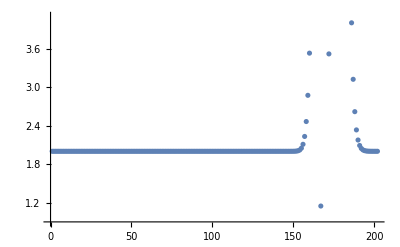

```mathematica
ListPlot[moment[0],PlotRange->{0.9,4.1}]
```

```mathematica
Dynamic[ListPlot[momentReference[0],PlotRange->{0.9,2.1}]]
Dynamic[momentReferenceSum[0]]
(*time: 26.7947376*)
FiniteVolumeSchemeReference[tend]
```

```mathematica
simulationValues=Table[{xs[i],moment[0][[i]],moment[1][[i]],moment[2][[i]]},{i,1,n}]//MatrixForm;
Export["shockTube_Relaxation1.0_Mesh100+300_spatiallyAdaptiveZero.txt",simulationValues,"CSV"]
```

shockTube_Relaxation1.0_Mesh100+300_spatiallyAdaptiveZero.txt

```mathematica
"shockTube_Relaxation1.0_Mesh100+300_spatiallyAdaptiveZero.txt"
```

shockTube_Relaxation1.0_Mesh250+250_spatiallyAdaptiveZero.txt

```mathematica
simulationReference=Table[{xs[i],momentReference[0][[i]],momentReference[1][[i]],momentReference[2][[i]]},{i,1,n}]//MatrixForm;
Export["shockTube_Relaxation1.0_Mesh100+300_Reference.txt",simulationValues,"CSV"]
```

shockTube_Relaxation1.0_Mesh100+300_Reference.txt

```mathematica
timeReference
```

26.7947

```mathematica
timeSpatiallyAdaptivePadded
```

19.303

#### Small linear profile + shock

```mathematica
(* Grid information *)
n=300;
x1=-2;
x2=1;

(* Domain decomposition info *)
domainDecompositionList=List[-1]; (* List of the physical positions where thwo models with different order are coupled *)
MomentsDomainDecomposition=List[4,6]; (* Number of moments in each part of the domain *)
paddingCondition="neighbour"; (* Padding condition for the boundary interface coupling *)

(*create grid cells *)
xs[i_]:=x1+dx*(i-0.5);

(* Choose initial values *)
m0[0,x_]:=Which[x<=0,3+x*0.2,x>0,1];
m0[1,x_]:=0;
m0[2,x_]:=0;
m0[3,x_]:=0;
m0[4,x_]:=0;
m0[5,x_]:=0;
m0[6,x_]:=0;
m0[7,x_]:=0;

(* Choose relaxation parameter *)
Relaxation[x_]:=1.0;

InitializeModel[]

(* Choose end time *)
tend=0.3;
```

```mathematica
Dynamic[ListPlot[moment[0],PlotRange->{0.9,3.3}]]
Dynamic[momentSum[0]]
(*time: 19.3030047*)
FiniteVolumeSchemePadded[tend]
```

```mathematica
DiscretizedDomainDecomposition
```

{100,300}

```mathematica
Dimensions[moment[0]]
```

{0}

```mathematica
timeSpatiallyAdaptivePadded
```

6.6981

```mathematica
Dynamic[ListPlot[momentReference[0],PlotRange->{0.9,3.3}]]
Dynamic[momentReferenceSum[0]]
(*time: 26.7947376*)
FiniteVolumeSchemeReference[tend]
```

```mathematica
timeReference
```

7.22676

```mathematica
Dynamic[ListPlot[momentLowOrder[0],PlotRange->{0.9,3.3}]]
Dynamic[momentLowOrderSum[0]]
(*time: 26.7947376*)
FiniteVolumeSchemeLowOrder[tend]
```

```mathematica
timeLowOrder
```

7.86442

```mathematica
simulationValues=Table[{xs[i],moment[0][[i]],moment[1][[i]],moment[2][[i]]},{i,1,n}]//MatrixForm;
Export["linear+shockTube_Relaxation10.0_Mesh100+200_spatiallyAdaptiveNeighbour_NewMatrix.txt",simulationValues,"CSV"];
simulationReference=Table[{xs[i],momentReference[0][[i]],momentReference[1][[i]],momentReference[2][[i]]},{i,1,n}]//MatrixForm;
Export["linear+shockTube_Relaxation10.0_Mesh100+200_Reference_NewMatrix.txt",simulationReference,"CSV"];
simulationLowOrder=Table[{xs[i],momentLowOrder[0][[i]],momentLowOrder[1][[i]],momentLowOrder[2][[i]]},{i,1,n}]//MatrixForm;
Export["linear+shockTube_Relaxation10.0_Mesh100+200_LowOrder_NewMatrix.txt",simulationLowOrder,"CSV"];
```

#### Non-square model

```mathematica
(* Choose number of cells in left and right subdomain *)
nxL = 100;
nxR = 200;

(* Choose boundaries of the spatial domain *)
x1=-2;
x2=1;

(*create grid cells *)
xs[i_]:=x1+dx*(i-0.5);

(* Choose number of moments in left and right subdomain *)
momentsLeft=4;
momentsRight=6;

(* Choose initial values *)
m0[0,x_]:=Which[x<=0,3+x*0.2,x>0,1];
m0[1,x_]:=0;
m0[2,x_]:=0;
m0[3,x_]:=0;
m0[4,x_]:=0;
m0[5,x_]:=0;
m0[6,x_]:=0;
m0[7,x_]:=0;

(* Choose relaxation parameter *)
Relaxation[x_]:=1.0;

InitializeModelNonSquare[nxL,nxR,x1,x2,momentsLeft,momentsRight]

(* Choose end time *)
tend=0.3;
```

```mathematica
Dynamic[ListPlot[moment[5],PlotRange->{0,0.01}]]
Dynamic[momentSum[0]]
FiniteVolumeSchemeNonSquareMatrices[tend]
```

```mathematica
Dimensions[SourceTermMatrixNonSquare]
```

{1610,1610}

```mathematica
Dimensions[BigAMatrixNonSquareMatrix]
```

{1610,1610}

```mathematica
Dimensions[Wraw]
```

{1610}

```mathematica
ViscosityBlockMatrix//MatrixForm
```

({{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
0 | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0},{0,-1,0},{0,0,-1}} | {{2,0,0},{0,2,0},{0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0},{0,-1,0},{0,0,-1},{0,0,0}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,0}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,1}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}} | {{2,0,0,0},{0,2,0,0},{0,0,2,0},{0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1},{0,0,0,0}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,0}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,1}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}} | {{2,0,0,0,0},{0,2,0,0,0},{0,0,2,0,0},{0,0,0,2,0},{0,0,0,0,2}} | {{-1,0,0,0,0},{0,-1,0,0,0},{0,0,-1,0,0},{0,0,0,-1,0},{0,0,0,0,-1}}
{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}} | {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}})

## Stability analysis

### Eigenvalues of the full spatial discretization matrix

```mathematica
(* Obtain the full spatial discretization matrix *)

StabilityMatrix = BigAMatrix-ArrayFlatten[SourceTermMatrixTest];
StabilityMatrixModified= BigAMatrixModified-ArrayFlatten[SourceTermMatrixTest];
StabilityMatrixReference= BigAMatrixReference-ArrayFlatten[SourceMatrixReference];
```

```mathematica
(* This computes the eigenvalues of the spatial discretization matrix *)

eigenvaluesStabilityMatrix=Eigenvalues[StabilityMatrix];
realPartEigenvalues =Re[eigenvaluesStabilityMatrix];
imaginaryPartEigenvalues  =Im[eigenvaluesStabilityMatrix ];
realPartEigenvaluesSorted=Sort[realPartEigenvalues];

eigenvaluesStabilityMatrixModified=Eigenvalues[StabilityMatrixModified];
realPartEigenvaluesModified =Re[eigenvaluesStabilityMatrixModified];
imaginaryPartEigenvaluesModified =Im[eigenvaluesStabilityMatrixModified];
realPartEigenvaluesModifiedSorted=Sort[realPartEigenvaluesModified];

eigenvaluesStabilityMatrixReference =Eigenvalues[StabilityMatrixReference];
realPartEigenvaluesReference =Re[eigenvaluesStabilityMatrixReference];
imaginaryPartEigenvaluesReference =Im[eigenvaluesStabilityMatrixReference];
realPartEigenvaluesReferenceSorted=Sort[realPartEigenvaluesReference];
```

```mathematica
(* This computes the eigenvalue with the biggest real part *)
Eigenvalues[StabilityMatrix,1,Method->{"Arnoldi","Criteria"->"RealPart","MaxIterations"->10000}]
```

Eigenvalues::maxit2: Warning: maximum number of iterations, 10000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{2.85577×10^-13}

#### Plotting

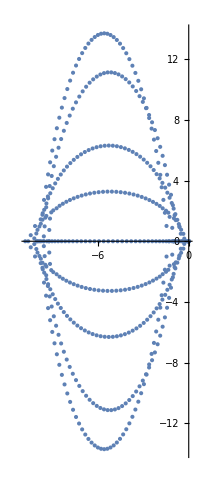

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrix]
```

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrixReference]
```

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

ComplexListPlot::ldata: Eigenvalues[{{0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 <<11>>e, <<498>>, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference, 0. - 2.5 RoeReference}, <<509>>}] is not a valid dataset or list of datasets.

ComplexListPlot[Eigenvalues[{{0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,461,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference,0.-2.5 RoeReference},508,{1}}]]
 |  |  |  |

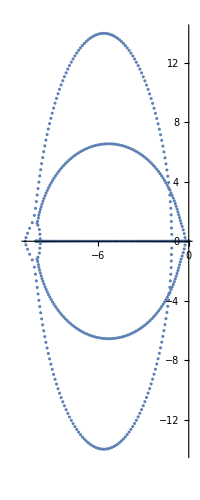

```mathematica
ComplexListPlot[eigenvaluesStabilityMatrixReference]
```

```mathematica
N[dx]
```

0.01

```mathematica
N[dt]
```

0.000666589

```mathematica
ALeft//MatrixForm
```

(0 | 1 | 0 | 0 | 0
1 | 0 | 2 | 0 | 0
0 | 1 | 0 | 3 | 0
0 | 0 | 1 | 0 | 4
0 | 0 | 0 | 1 | 0)